```mathematica
$Assumptions={sp>0,s>0,sp+q2>0,t1>0,m2>0,q2<0,s4>0,
0<ρ,ρ<1,0<β,β<1,0<χ,χ<1,
ρq<0,βq>1,0<χq<1,
0<ρp,ρp<ρq/(ρq-1),ρp<ρ,ρp<1,ρp ρq/(ρq+ρp)>0,ρ ρq/(ρq-ρ)>0,
0<βp,βp<1,0<χp,χq<χp,χp<1,β<βp,χ>χp,
δ>0
}/.List->And
```

sp>0&&s>0&&q2+sp>0&&t1>0&&m2>0&&q2<0&&s4>0&&0<ρ&&ρ<1&&0<β&&β<1&&0<χ&&χ<1&&ρq<0&&βq>1&&0<χq<1&&0<ρp&&ρp<ρq/(-1+ρq)&&ρp<ρ&&ρp<1&&(ρp ρq)/(ρp+ρq)>0&&(ρ ρq)/(-ρ+ρq)>0&&0<βp&&βp<1&&0<χp&&χq<χp&&χp<1&&β<βp&&χ>χp&&δ>0

## A2L

### psLog3b

```mathematica
IntIntAL2[psLog3b][raw]={((4 π q2 (m2+sp+t1+u1) (-4 m2^2 (4 q2+5 sp)+(q2-t1-u1) (q2 (-sp+t1)+sp u1-2 t1 (t1+u1))+2 m2 (2 q2^2+sp^2+q2 (2 sp-7 t1-4 u1)-sp (3 t1+u1)+(t1+u1) (3 t1+2 u1))))/(sp^2 (sp+t1+u1) (-4 m2 (q2+sp)+(-q2+t1+u1)^2)^(3/2))),
(2 m2 (q2+sp)+(sp+t1+u1) (q2-t1-u1+Sqrt[-4 m2 (q2+sp)+(-q2+t1+u1)^2]))/(2 m2 (q2+sp)-(sp+t1+u1) (-q2+t1+u1+Sqrt[-4 m2 (q2+sp)+(-q2+t1+u1)^2]))};
Module[{c,l,psN},
{c,l}=IntIntAL2[psLog3b][raw];
psN=(1/(2π) (*Kqγ NC CF*) (s4/(s4+m2)));
c=FullSimplify[psN c (m2(*/(4π)*)) 1/sp^2/.{u1-> s4-sp-t1}];
l=FullSimplify[l/.{u1-> s4-sp-t1}];
IntIntAL2[psLog3b][coeffs]={c,l}
]
```

{-(2 m2 q2 (4 m2^2 (4 q2+5 sp)-2 m2 (2 q2^2+2 s4^2-5 s4 sp+4 sp^2+q2 (-4 s4+6 sp-3 t1)+s4 t1-3 sp t1)+(q2-s4+sp) (sp (q2-s4+sp)-(q2-2 s4+sp) t1)))/(sp^4 (-4 m2 (q2+sp)+(q2-s4+sp)^2)^(3/2)),(2 m2 (q2+sp)+s4 (q2-s4+sp+√(-4 m2 (q2+sp)+(q2-s4+sp)^2)))/(2 m2 (q2+sp)+s4 (q2-s4+sp-√(-4 m2 (q2+sp)+(q2-s4+sp)^2)))}

```mathematica
Module[{s4max,norm,p,t1min,t1max,wmin},
norm={sp-> s-q2,β-> Sqrt[1-ρ],ρ->4m2/s};
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2);
Print@FullSimplify[(s-s4max)/s/.{β->Sqrt[1-ρ]}]
]
```

-t1/sp-(sp ρ)/(4 t1)

```mathematica
Solve[{s4==s(1-(1+w^2)/(2w) Sqrt@ρ)},w]//FullSimplify
```

{{w→(s-s4-√((s-s4)^2-s^2 ρ))/(s √ρ)},{w→(s-s4+√((s-s4)^2-s^2 ρ))/(s √ρ)}}

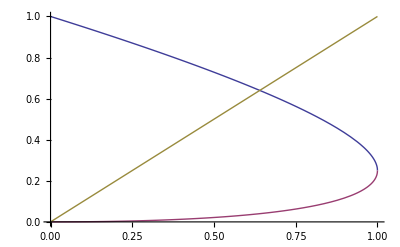

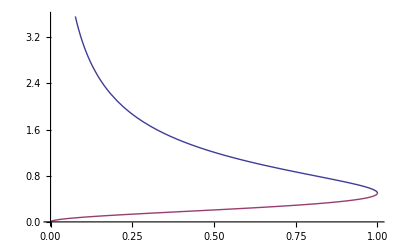

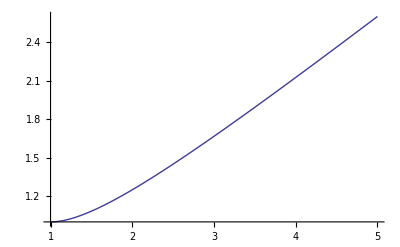

```mathematica
Plot[{((1+Sqrt[1-ρ])/2)^2,((1-Sqrt[1-ρ])/2)^2,ρ},{ρ,0,1}]
Plot[{((1+Sqrt[1-ρ])/2)/Sqrt@ρ,((1-Sqrt[1-ρ])/2)/Sqrt@ρ},{ρ,0,1}]
Plot[(1+w^2)/(2 w),{w,1,5}]
```

```mathematica
Module[{c,l,sol,jac,t,I,s4min,wmin,s4max,wmax,wmax1,wmax2,Ilower,Iupper1,Iupper2},
{c,l}=IntIntAL2[psLog3b][coeffs];
t={q2-> 4m2/ρq,sp-> 4m2/ρp,s-> 4m2/ρ,s4-> s(1-(1+w^2)/(2w)Sqrt@ρ),t1-> -sp/2v};
t=Map[First@#-> (Last@#//.t)&,t];
sol=Solve[{s4==s(1-(1+w^2)/(2w) Sqrt@ρ)},w]//FullSimplify;
Print@t;
jac=(-s Sqrt[ρ]D[(1+w^2)/(2w),w]) * (- sp/2);
{c,l}=FullSimplify[FullSimplify[{c jac,l}/.{sp-> s-q2}/.t,Assumptions-> {w>1,m2>0,1>ρ>0}]/.{ρ-ρq-> -ρ ρq/ρp}];
Print@{c,l};
I=Integrate[c  Log@l,w];
I=Collect[I,{Log[_],PolyLog[_,_]},Simplify];
Print@I;
s4min=0;
wmin=FullSimplify[FullSimplify[(w/.Last@sol/.{s4-> s4min})/.t]/.{Sqrt[1-ρ]-> β}];
Print["wmin = ",wmin];
Ilower=Limit[I,w-> wmin];
(*Print@Ilower;*)
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2);
wmax=FullSimplify[FullSimplify[(w/.Last@sol/.{s4-> s4max})/.t]/.{β^2-> 1-ρ},Assumptions-> {v>0,ρ>0}];
wmax1=Refine[wmax,v<Sqrt[ρ]&&v>0];
wmax2=Refine[wmax,v≥ Sqrt@ρ];
Print["wmax = ",wmax," => ",{wmax1,wmax2}];
Iupper1=Limit[I,w-> wmax1];
(*Print@Iupper1;*)
Iupper2=Limit[I,w-> wmax2];
(*Print@Iupper2;*)
{Ilower,Iupper1,Iupper2}={Ilower,Iupper1,Iupper2}/.{Log[4]-> ln[4]}//.{Log[a_]+Log[b_]:>Log[a b ],Log[a_]-Log[b_]:>Log[a /b ],Log[1/a_]:> -Log[a]};
IntIntAL2[psLog3b][Is]={Ilower,Iupper1,Iupper2}
]
```

{q2→(4 m2)/ρq,sp→(4 m2)/ρp,s→(4 m2)/ρ,s4→(4 m2 (1-((1+w^2) √ρ)/(2 w)))/ρ,t1→-(2 m2 v)/ρp}

{(ρp^2 (2 w^2 ρ^2 ρp-2 (1+w^4) ρp ρq+2 w (1+w^2) √ρ (v+ρp) ρq-(w+w^3) ρ^(3/2) (2 ρp-v ρq)+2 ρ (-v (1+w^4) ρq+ρp (1+ρq-3 w^2 ρq+w^4 (1+ρq)))))/(8 w (-1+w^2)^2 ρ ρq^2),(w^3 (-2+w √ρ))/(-2 w+√ρ)}

(3 (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[1-w])/(16 ρ ρq^2)+((4-2 √ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+w])/(16 (-2+√ρ) ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[w]^2)/(8 ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[1+w])/(4 (2+√ρ) ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[2+2 (-1+w)-√ρ])/(8 (-2+√ρ) ρ ρq^2)+Log[w-(√ρ)/2] ((ρp^2 (2 (v+ρp) ρq+ρ (-2 ρp+v ρq)) Log[1-(w-(√ρ)/2)/(-1-(√ρ)/2)])/(32 √ρ ρq^2)+(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) Log[1-(w-(√ρ)/2)/(1-(√ρ)/2)])/(32 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1+(2 (w-(√ρ)/2))/(√ρ)])/(4 ρ ρq^2)-(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) Log[(2 (-1+w))/(-2+√ρ)])/(32 ρ ρq^2)+(ρp^2 (-2 (v+ρp) ρq+ρ (2 ρp-v ρq)) Log[(2 (1+w))/(2+√ρ)])/(32 √ρ ρq^2))+((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[-2 w+√ρ])/(8 (2+√ρ) ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[2-w √ρ])/(16 (-2+√ρ) √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[2+√ρ-(1+w) √ρ])/(16 (2+√ρ) √ρ ρq^2)-(ρp^2 (ρ^2 ρp-2 ρp ρq+2 w √ρ (v+ρp) ρq+w ρ^(3/2) (-2 ρp+v ρq)-ρ (ρp (-2+ρq)+2 v ρq)) Log[-(2 w^3)/(-2 w+√ρ)+(w^4 √ρ)/(-2 w+√ρ)])/(8 (-1+w^2) ρ ρq^2)+Log[1-w^2] ((ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[w-2/(√ρ)])/(8 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[w-(√ρ)/2])/(8 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[-(2 w^3)/(-2 w+√ρ)+(w^4 √ρ)/(-2 w+√ρ)])/(8 ρ ρq^2))+Log[-1+w^2] ((ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[w-2/(√ρ)])/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[w-(√ρ)/2])/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-(2 w^3)/(-2 w+√ρ)+(w^4 √ρ)/(-2 w+√ρ)])/(8 ρ ρq^2))+Log[w] (-(3 ρp^2 (ρ^2 ρp-2 ρp ρq-ρ (ρp (-2+ρq)+2 v ρq)))/(8 ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-w^2])/(8 ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-1+w^2])/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[w-(√ρ)/2])/(4 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-(w √ρ)/2])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-(2 w^3)/(-2 w+√ρ)+(w^4 √ρ)/(-2 w+√ρ)])/(4 ρ ρq^2))+(ρp^2 (2 (v+ρp) ρq+ρ (-2 ρp+v ρq)) PolyLog[2,(w-(√ρ)/2)/(-1-(√ρ)/2)])/(32 √ρ ρq^2)+(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(w-(√ρ)/2)/(1-(√ρ)/2)])/(32 ρ ρq^2)-(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(-2 w+√ρ)/(-2+√ρ)])/(32 ρ ρq^2)+(ρp^2 (-2 (v+ρp) ρq+ρ (2 ρp-v ρq)) PolyLog[2,(-2 w+√ρ)/(2+√ρ)])/(32 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,-(2 (w-(√ρ)/2))/(√ρ)])/(4 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(w √ρ)/2])/(4 ρ ρq^2)

wmin = (1+β)/(√ρ)

wmax = Piecewise[{{v/(√ρ), v^2≥ρ}, {(√ρ)/v, True}}] => {(√ρ)/v,v/(√ρ)}

{-((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[1-β])/(16 (2+√ρ) √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[1-β])/(16 (-2+√ρ) √ρ ρq^2)+((4-2 √ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+(1+β)/(√ρ)])/(16 (-2+√ρ) ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(1+β)/(√ρ)]^2)/(8 ρ ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) (ⅈ π+Log[-(-1-β+√ρ)/(√ρ)]))/(16 ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[(1+β+√ρ)/(√ρ)])/(4 (2+√ρ) ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[(2+2 β-ρ)/(√ρ)])/(8 (-2+√ρ) ρ ρq^2)+(3 ρp^2 Log[(1+β)/(√ρ)] (-2 ρ ρp+ⅈ π ρ ρp-ρ^2 ρp+2 v ρ ρq-ⅈ π v ρ ρq+2 ρp ρq-ⅈ π ρp ρq+ρ ρp ρq+ⅈ π ρ ρp ρq+2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1+β]+(ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[ρ]))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(1+2 β+β^2-ρ)/ρ] (-ⅈ π+3 Log[1+β]-Log[2 ρ]))/(8 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) (π-ⅈ Log[(1+2 β+β^2-ρ)/ρ]) (π-ⅈ Log[(2 ρ)/(1+β)^3]))/(8 ρ ρq^2)-(ρp^2 (ρ^2 ρp+2 v ρq-ρ (v+ρp) ρq+β (2 (v+ρp) ρq+ρ (-2 ρp+v ρq))) Log[((-1+β) (1+β)^3)/(ρ (-2-2 β+ρ))])/(8 (1+2 β+β^2-ρ) ρq^2)+((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) (ⅈ π+Log[-(-2-2 β+ρ)/(√ρ)]))/(8 (2+√ρ) ρ ρq^2)+Log[(2+2 β-ρ)/(2 √ρ)] (-(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) (ⅈ π+Log[-(2 (-1+(1+β)/(√ρ)))/(-2+√ρ)]))/(32 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(2 (1+β))/ρ])/(4 ρ ρq^2)+(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) (ⅈ π+Log[-(2 (1+β-√ρ))/(-2 √ρ+ρ)]))/(32 ρ ρq^2)+(ρp^2 (-2 (v+ρp) ρq+ρ (2 ρp-v ρq)) Log[(2 (1+β+√ρ))/(2 √ρ+ρ)])/(32 √ρ ρq^2)+(ρp^2 (2 (v+ρp) ρq+ρ (-2 ρp+v ρq)) Log[(2 (1+β+√ρ))/(2 √ρ+ρ)])/(32 √ρ ρq^2))-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(1+β)/2])/(4 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(-2-2 β+ρ)/ρ])/(4 ρ ρq^2)+(ρp^2 (-2 (v+ρp) ρq+ρ (2 ρp-v ρq)) PolyLog[2,(-2-2 β+ρ)/(2 √ρ+ρ)])/(32 √ρ ρq^2)+(ρp^2 (2 (v+ρp) ρq+ρ (-2 ρp+v ρq)) PolyLog[2,(-2-2 β+ρ)/(2 √ρ+ρ)])/(32 √ρ ρq^2),(3 (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[1-(√ρ)/v])/(16 ρ ρq^2)+((4-2 √ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+(√ρ)/v])/(16 (-2+√ρ) ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[1+(√ρ)/v])/(4 (2+√ρ) ρ ρq^2)-(3 ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(√ρ)/v]^2)/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-((-2+v) √ρ)/v])/(8 (-2+√ρ) ρ ρq^2)+(-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[2/v])/(4 ρ ρq^2)+(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) (-Log[2]-Log[(-v+√ρ)/(v (-2+√ρ))]))/(32 ρ ρq^2)+(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) Log[(2 (-v+√ρ))/(v (-2+√ρ))])/(32 ρ ρq^2)+(ρp^2 (2 (v+ρp) ρq+ρ (-2 ρp+v ρq)) Log[(2 (v+√ρ))/(v (2+√ρ))])/(32 √ρ ρq^2)+(ρp^2 (-2 (v+ρp) ρq+ρ (2 ρp-v ρq)) Log[(2 (1+(√ρ)/v))/(2+√ρ)])/(32 √ρ ρq^2)) Log[-((-2+v) √ρ)/(2 v)]+((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[((-2+v) √ρ)/v])/(8 (2+√ρ) ρ ρq^2)-(v^2 ρp^2 (2 ρ ρp+ρ^2 ρp-(2 ρ^2 ρp)/v+2 ρ ρq-2 v ρ ρq+ρ^2 ρq-2 ρp ρq-ρ ρp ρq+(2 ρ ρp ρq)/v) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ (-v^2+ρ) ρq^2)+(-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2 v+ρ)/(v √ρ)])/(8 ρ ρq^2)) Log[1-ρ/v^2]+((ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2 v+ρ)/(v √ρ)])/(8 ρ ρq^2)) Log[-1+ρ/v^2]-((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[2-ρ/v])/(16 (2+√ρ) √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[2-ρ/v])/(16 (-2+√ρ) √ρ ρq^2)+Log[(√ρ)/v] (-(3 ρp^2 (ρ^2 ρp-2 ρp ρq-ρ (ρp (-2+ρq)+2 v ρq)))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-((-2+v) √ρ)/(2 v)])/(4 ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-ρ/v^2])/(8 ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-1+ρ/v^2])/(8 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-ρ/(2 v)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(-2 v ρ+ρ^2)/((-2+v) v^3)])/(4 ρ ρq^2))-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,(-2+v)/v])/(4 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,ρ/(2 v)])/(4 ρ ρq^2),-((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[2-v])/(16 (2+√ρ) √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[2-v])/(16 (-2+√ρ) √ρ ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[1-v/(√ρ)])/(16 ρ ρq^2)+((4-2 √ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+v/(√ρ)])/(16 (-2+√ρ) ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[1+v/(√ρ)])/(4 (2+√ρ) ρ ρq^2)-(ρp^2 (2 ρ ρp-2 v ρ ρp+ρ^2 ρp+2 v^2 ρq-2 v ρ ρq+v^2 ρ ρq-2 ρp ρq+2 v ρp ρq-ρ ρp ρq) Log[(2 v^3-v^4)/((2 v-ρ) ρ)])/(8 (v^2-ρ) ρq^2)-(3 ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[v/(√ρ)]^2)/(8 ρ ρq^2)+((ρp^2 (-2 (v+ρp) ρq+ρ (2 ρp-v ρq)) Log[(2 (1+v/(√ρ)))/(2+√ρ)])/(32 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(2 v)/ρ])/(4 ρ ρq^2)+(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) (-Log[2]-Log[(v-√ρ)/((-2+√ρ) √ρ)]))/(32 ρ ρq^2)+(ρp^2 (4 ρp ρq-2 √ρ (v+ρp) ρq+ρ^(3/2) (2 ρp-v ρq)-4 ρ (ρp-v ρq+ρp ρq)) Log[(2 (v-√ρ))/((-2+√ρ) √ρ)])/(32 ρ ρq^2)+(ρp^2 (2 (v+ρp) ρq+ρ (-2 ρp+v ρq)) Log[(2 (v+√ρ))/((2+√ρ) √ρ)])/(32 √ρ ρq^2)) Log[(2 v-ρ)/(2 √ρ)]+Log[1-v^2/ρ] (-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(2 v^3-v^4)/((2 v-ρ) ρ)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2+v)/(√ρ)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(2 v-ρ)/(2 √ρ)])/(8 ρ ρq^2))+Log[-1+v^2/ρ] ((ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(2 v^3-v^4)/((2 v-ρ) ρ)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2+v)/(√ρ)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(2 v-ρ)/(2 √ρ)])/(8 ρ ρq^2))+Log[v/(√ρ)] (-(3 ρp^2 (ρ^2 ρp-2 ρp ρq-ρ (ρp (-2+ρq)+2 v ρq)))/(8 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-v/2])/(4 ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-v^2/ρ])/(8 ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-1+v^2/ρ])/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(2 v^3-v^4)/((2 v-ρ) ρ)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(2 v-ρ)/(2 √ρ)])/(4 ρ ρq^2))-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[(2 v-ρ)/(√ρ)])/(8 (-2+√ρ) ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[(-2 v+ρ)/(√ρ)])/(8 (2+√ρ) ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,v/2])/(4 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,(-2 v+ρ)/ρ])/(4 ρ ρq^2)}

```mathematica
Module[{Ilower,Iupper1,Iupper2,c},
{Ilower,Iupper1,Iupper2}=IntIntAL2[psLog3b][Is];
c=Integrate[Ilower,{v,(1+β)/Sqrt@ρ,(1-β)/Sqrt@ρ}];
IntIntAL2[psLog3b][JlowerRes]=c
]
```

1/(8 ρq^2)β ρp^2 ((2 ((-2+ρ) √ρ ρp (ρ-ρq)+4 ρq) Log[1-β])/((-4+ρ) ρ)-(3 ⅈ (2-2 √ρ+ρ) (ρ ρp+ρq-ρp ρq) (π-ⅈ Log[-1+(1+β)/(√ρ)]))/ρ^(3/2)-((4+(-2+ρ) √ρ) (ρ ρp+ρq-ρp ρq) Log[-1+(1+β)/(√ρ)])/(-2 ρ^(3/2)+ρ^2)-(4 (2+4 √ρ+3 ρ+ρ^(3/2)) (ρ ρp-(1+ρp) ρq) Log[1+(1+β)/(√ρ)])/(2 ρ^(3/2)+ρ^2)+(2 (-ρ^(3/2) (-2 β+ρ) ρp+(-2+ρ-β (2+ρ)+√ρ (-2 β+ρ) ρp) ρq) Log[-((-1+β) (1+β)^3)/((2+2 β-ρ) ρ)])/(ρ (-(1+β)^2+ρ))+(6 (-√ρ ρq-ρp ρq+ρ ρp (1+ρq)) Log[(1+β)/(√ρ)]^2)/ρ^(3/2)+(4 (-√ρ ρq-ρp ρq+ρ ρp (1+ρq)) Log[(2 (1+β))/ρ] Log[(2+2 β-ρ)/(2 √ρ)])/ρ^(3/2)+(2 (2-2 √ρ+ρ) (ρ ρp+ρq-ρp ρq) Log[(2+2 β-ρ)/(√ρ)])/(-2 ρ^(3/2)+ρ^2)+(6 Log[(1+β)/(√ρ)] (ρ (2-ⅈ π+ρ) ρp+ⅈ ((2 ⅈ+π) √ρ+(π-π ρ+ⅈ (2+ρ)) ρp) ρq-(-√ρ ρq-ρp ρq+ρ ρp (1+ρq)) (2 Log[1+β]-Log[ρ])))/ρ^(3/2)+(2 (-√ρ ρq-ρp ρq+ρ ρp (1+ρq)) Log[-1+(1+β)^2/ρ] (ⅈ π+Log[2]-3 Log[1+β]+Log[ρ]))/ρ^(3/2)+((2+2 √ρ+ρ) (ρ ρp-(1+ρp) ρq) (-2 ⅈ π-2 Log[2+2 β-ρ]+Log[ρ]))/(2 ρ^(3/2)+ρ^2)+(2 (-√ρ ρq-ρp ρq+ρ ρp (1+ρq)) (π-ⅈ Log[-1+(1+β)^2/ρ]) (π-ⅈ Log[(2 ρ)/(1+β)^3]))/ρ^(3/2)+(4 ρp PolyLog[2,(1+β)/2])/(√ρ)-(4 ρq PolyLog[2,(1+β)/2])/ρ-(4 ρp ρq PolyLog[2,(1+β)/2])/ρ^(3/2)+(4 ρp ρq PolyLog[2,(1+β)/2])/(√ρ)+(4 (-√ρ ρq-ρp ρq+ρ ρp (1+ρq)) PolyLog[2,(-2-2 β+ρ)/ρ])/ρ^(3/2))

```mathematica
Module[{Ilower,Iupper1,Iupper2,c},
{Ilower,Iupper1,Iupper2}=IntIntAL2[psLog3b][Is];
Print@Iupper1;
c=Integrate[Iupper1,v];
c=TrigToExp[c]/.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]};
c=c/.{ln[a_]+ln[b_]:>ln[Simplify[a b]]};
c=Collect[c,{ln[_],Li2[_]},FullSimplify];
IntIntAL2[psLog3b][Jupper1Raw]=c
]
```

(3 (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[1-(√ρ)/v])/(16 ρ ρq^2)+((2+√ρ) (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+(√ρ)/v])/(16 (-2+√ρ) ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[1+(√ρ)/v])/(4 (2+√ρ) ρ ρq^2)-(3 ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(√ρ)/v]^2)/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-((-2+v) √ρ)/v])/(8 (-2+√ρ) ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[((-2+v) √ρ)/v])/(8 (2+√ρ) ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)] (2 Log[2]+2 Log[(√ρ)/v]-Log[ρ]))/(8 ρ ρq^2)-(v^2 ρp^2 (2 ρ ρp+ρ^2 ρp-(2 ρ^2 ρp)/v+2 ρ ρq-2 v ρ ρq+ρ^2 ρq-2 ρp ρq-ρ ρp ρq+(2 ρ ρp ρq)/v) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ (-v^2+ρ) ρq^2)+(-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2 v+ρ)/(v √ρ)])/(8 ρ ρq^2)) Log[1-ρ/v^2]+((ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2 v+ρ)/(v √ρ)])/(8 ρ ρq^2)) Log[-1+ρ/v^2]-(ρp^2 (-2 ρ ρp+ρ^2 ρp+4 v ρq+2 ρp ρq-ρ ρp ρq) Log[2-ρ/v])/(8 (-4+ρ) ρq^2)+Log[(√ρ)/v] (-(3 ρp^2 (ρ^2 ρp-2 ρp ρq-ρ (ρp (-2+ρq)+2 v ρq)))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-((-2+v) √ρ)/(2 v)])/(4 ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-ρ/v^2])/(8 ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-1+ρ/v^2])/(8 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-ρ/(2 v)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(-2 v ρ+ρ^2)/((-2+v) v^3)])/(4 ρ ρq^2))-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,(-2+v)/v])/(4 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,ρ/(2 v)])/(4 ρ ρq^2)

(ρp^2 (4 ρ (12 v+(-4+ρ) (2+ρ)) ρp+(ρ (-6 v^2+(-4+ρ)^2+2 v (8+7 ρ))+4 (12 v (-1+ρ)-(-4+ρ) (2+ρ)) ρp) ρq))/(64 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[1-2/v])/(8 ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+v)/(-2-√ρ)])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+v)/(-2+√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(v-ρ/2)/(-√ρ-ρ/2)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(v-ρ/2)/(√ρ-ρ/2)])/(16 √ρ ρq^2)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-v/(√ρ)])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[v/(√ρ)])/(16 √ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[ρ/(2 v)])/(8 ρ ρq^2)+ln[2] ((v ρp^2)/(4 ρq)+(ρp^2 (ρq+ρp (-1+(-1+1/ρ) ρq)) ln[-2+v])/(2 ρq^2))-((-1+√ρ) (2-2 √ρ+ρ) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v-√ρ])/(8 (-2+√ρ) √ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v+√ρ])/(8 (2+√ρ) √ρ ρq^2)-(v (2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρ ρp+v √ρ ρq+2 ρp ρq) ln[(v+√ρ)/v])/(8 (2+√ρ) ρ ρq^2)+(3 v (2-2 √ρ+ρ) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[1-(√ρ)/v])/(32 ρ ρq^2)+(v (4+(-2+ρ) √ρ) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[-1+(√ρ)/v])/(32 (-2+√ρ) ρ ρq^2)-(v^2 ρp^2 ln[1/2 (2 v-ρ)])/(8 ρq)+(ρp^2 (4 ρ (8+(-4+ρ) ρ) ρp+(ρ^2 (-8+3 ρ)-4 (8+3 (-4+ρ) ρ) ρp) ρq) ln[2 v-ρ])/(64 (-4+ρ) ρq^2)+ln[v] ((3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-v/(√ρ)])/(8 ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+v/(√ρ)])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v^2-ρ])/(8 ρq^2))+((ρp^2 (2 v^2 ρq-(2+ρ) (-ρp ρq+ρ (ρp+ρq))))/(16 ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(v-ρ/2)/(-√ρ-ρ/2)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(v-ρ/2)/(√ρ-ρ/2)])/(16 √ρ ρq^2)) ln[v-ρ/2]+ln[2-v] ((ρp^2 (2 ρ ρp+(ρ+2 (-5+ρ) ρp) ρq))/(4 (-4+ρ) ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+(-1+ρp) ρq)) ln[4/ρ])/(4 ρ ρq^2))-(v ρp^2 ln[√ρ])/(4 ρq)+ln[-2+v] (((-2+v) ρp^2 (-2 ρ ρp+2 ρp ρq+ρ (v+ρp) ρq-ρ^2 (ρp+ρq)))/(8 ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(-2+v)/(-2-√ρ)])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(-2+v)/(-2+√ρ)])/(16 √ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+(-1+ρp) ρq)) ln[√ρ])/(2 ρ ρq^2))+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(√ρ)/v]^2)/(16 ρ ρq^2)-(v (2-2 √ρ+ρ) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[-((-2+v) √ρ)/v])/(16 (-2+√ρ) ρ ρq^2)+ln[4/ρ] (-(v ρp^2)/(8 ρq)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-((-2+v) √ρ)/(2 v)])/(16 ρ ρq^2))-(v (2+2 √ρ+ρ) ρp^2 (-2 ρ ρp+v √ρ ρq+2 ρp ρq) ln[((-2+v) √ρ)/v])/(16 (2+√ρ) ρ ρq^2)+(v ρp^2 (ρ (2+ρ) ρp+(ρ^2-2 ρp-ρ (-2+v+ρp)) ρq) ln[(ρ (-2 v+ρ))/v^3])/(8 ρ ρq^2)+ln[v^2-ρ] ((ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(8 ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(ρ (-2 v+ρ))/v^3])/(8 ρq^2))+ln[1+v/(√ρ)] (((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(ρ (-2 v+ρ))/v^3])/(16 √ρ ρq^2))+ln[1-v/(√ρ)] (-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(ρ (-2 v+ρ))/v^3])/(16 √ρ ρq^2))-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(-2 v+ρ)/(v √ρ)] ln[1-ρ/v^2])/(16 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(-2 v+ρ)/(v √ρ)] ln[-1+ρ/v^2])/(16 ρ ρq^2)+ln[-((-2+v) √ρ)/(2 v)] ((v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[1-ρ/v^2])/(16 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-1+ρ/v^2])/(16 ρ ρq^2))+ln[(ρ (-2 v+ρ))/((-2+v) v^3)] (-(v ρp^2 (4 ρp ρq+ρ (v ρq-4 ρp (1+ρq))))/(16 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[1-ρ/v^2])/(16 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-1+ρ/v^2])/(16 ρ ρq^2))+(v ρp^2 (-(-2+ρ) ρp (ρ-ρq)-2 v ρq) ln[2-ρ/v])/(8 (-4+ρ) ρq^2)+ln[(√ρ)/v] ((3 v ρp^2 (-ρ (2+ρ) ρp+(v ρ+(2+ρ) ρp) ρq))/(8 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(ρ (-2 v+ρ))/((-2+v) v^3)])/(8 ρ ρq^2)-(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[1-ρ/v^2])/(16 ρ ρq^2)+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-1+ρ/v^2])/(16 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[1-ρ/(2 v)])/(8 ρ ρq^2))

```mathematica
Module[{I,a,b,c},
I=IntIntAL2[psLog3b][Jupper1Raw];
a=I/.{v-> Sqrt@ρ};
b=I/.{v-> (1-β)/Sqrt@ρ};
c=a-b;
c=c/.{ln[z_]:>ln@FullSimplify@z,Li2[z_]:>Li2@FullSimplify@z};
c=c/.{ln@1-> 0};
c=Collect[c,{ln[_],Li2@_},FullSimplify];
IntIntAL2[psLog3b][Jupper1Res]=c
]
```

((-1+β+ρ) ρp^2 (24 ρ ρp+(3 (-1+β) √ρ+8 ρ-3 ρ^(3/2)+7 ρ^2+24 (-1+ρ) ρp) ρq))/(32 ρ^(3/2) ρq^2)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1-4/(2+√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1+4/(2+√ρ)])/(16 √ρ ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) Li2[1-2/(√ρ)])/(8 √ρ ρq^2)-((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) Li2[1+(2 √ρ)/(-1+β)])/(8 ρ^(3/2) ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1-β)/ρ])/(16 √ρ ρq^2)-(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-1+β)/ρ])/(16 √ρ ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) Li2[(√ρ)/2])/(8 √ρ ρq^2)-((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) Li2[ρ^(3/2)/(2-2 β)])/(8 ρ^(3/2) ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-(-1+β+2 √ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-1+β+2 √ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+2 β+ρ^(3/2))/((-2+√ρ) ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+2 β+ρ^(3/2))/((2+√ρ) ρ)])/(16 √ρ ρq^2)+(ρp^2 (-4 ρ (8+(-4+ρ) ρ) ρp+((8-3 ρ) ρ^2+4 (8+3 (-4+ρ) ρ) ρp) ρq) ln[-(2 (-1+β))/(√ρ)-ρ])/(64 (-4+ρ) ρq^2)+(ρp^2 (4 ρ (8+(-4+ρ) ρ) ρp+(ρ^2 (-8+3 ρ)-4 (8+3 (-4+ρ) ρ) ρp) ρq) ln[2 √ρ-ρ])/(64 (-4+ρ) ρq^2)+(-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)))/(16 ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[4/(2+√ρ)])/(16 √ρ ρq^2)) ln[√ρ-ρ/2]+ln[2+(-1+β)/(√ρ)] (-(ρp^2 (2 ρ ρp+(ρ+2 (-5+ρ) ρp) ρq))/(4 (-4+ρ) ρq^2)+(ρp^2 (ρp ρq-ρ (ρp+(-1+ρp) ρq)) ln[4/ρ])/(4 ρ ρq^2))+ln[2-√ρ] (-(ρp^2 (2 ρ^3 ρp-8 ρp ρq+44 √ρ ρp ρq-2 ρ^2 ρp (2+ρq)+ρ^(5/2) (2 ρp+ρq)+4 ρ (ρq+ρp (2+ρq))-2 ρ^(3/2) (ρq+ρp (6+5 ρq))))/(16 (-4+ρ) √ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+(-1+ρp) ρq)) ln[4/ρ])/(4 ρ ρq^2))-((-1+β+ρ) ρp^2 ln[√ρ])/(4 √ρ ρq)+ln[2] ((ρp^2 (2 (-1+β) ρq+2 ρ ρq+((2+4 √ρ+3 ρ+ρ^(3/2)) (2 ρ ρp-(ρ+2 ρp) ρq))/(2+√ρ)))/(8 √ρ ρq^2)-(ρp^2 (ρq+ρp (-1+(-1+1/ρ) ρq)) ln[-2+(1-β)/(√ρ)])/(2 ρq^2)+(ρp^2 (-((2+ρ) (-ρp ρq+ρ (ρp+ρq)))/(√ρ)+8 (ρq+ρp (-1+(-1+1/ρ) ρq))) ln[-2+√ρ])/(16 ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ-ρ/2])/(16 √ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ])/(8 ρq^2))+ln[-2+√ρ] ((ρp^2 (4 ρ ρp (4-3 ρq)-16 ρp ρq-12 √ρ ρp ρq+6 ρ^2 (2 ρp+ρq)+3 ρ^(5/2) (2 ρp+ρq)-2 ρ^(3/2) (3 ρp (-2+ρq)+ρq)))/(16 (2+√ρ) ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-4/(2+√ρ)])/(16 √ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+(-1+ρp) ρq)) ln[√ρ])/(2 ρ ρq^2))+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[2 √ρ])/(8 (2+√ρ) √ρ ρq^2)-(3 (-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-ρ/(-1+β)]^2)/(16 ρ^(3/2) ρq^2)-((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[(1-β+ρ)/(√ρ)])/(8 (2+√ρ) √ρ ρq^2)+ln[(1-β)/(√ρ)] (-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1-β+ρ)/ρ])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(-1+β+ρ)/ρ])/(8 ρq^2))+((-1+√ρ) (2-2 √ρ+ρ) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[-(-1+β+ρ)/(√ρ)])/(8 (-2+√ρ) √ρ ρq^2)+ln[-2+(1-β)/(√ρ)] (-((-1+β+2 √ρ) ρp^2 (ρ (2+ρ) ρp+((-1+β) √ρ+ρ^2-(2+ρ) ρp) ρq))/(8 ρ^(3/2) ρq^2)+(ρp^2 (ρp ρq-ρ (ρp+(-1+ρp) ρq)) ln[√ρ])/(2 ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(-1+β+ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1-β+ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2))+((-1+β) (2-2 √ρ+ρ) ρp^2 (-2 ρ ρp+(-1+β+2 ρp) ρq) ln[-√ρ-(2 ρ)/(-1+β)])/(16 (-2+√ρ) ρ^(3/2) ρq^2)+((-1+β) (4+(-2+ρ) √ρ) ρp^2 (2 ρ ρp-(-1+β+2 ρp) ρq) ln[-1-ρ/(-1+β)])/(32 (-2+√ρ) ρ^(3/2) ρq^2)+((-1+β) (2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+(-1+β-2 ρp) ρq) ln[1-ρ/(-1+β)])/(8 (2+√ρ) ρ^(3/2) ρq^2)+ln[4/ρ] (-((-1+β+ρ) ρp^2)/(8 √ρ ρq)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[1-(√ρ)/2])/(16 √ρ ρq^2)-((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-(√ρ)/2-ρ/(-1+β)])/(16 ρ^(3/2) ρq^2))-(3 (-1+β) (2-2 √ρ+ρ) ρp^2 (-2 ρ ρp+(-1+β+2 ρp) ρq) ln[1+ρ/(-1+β)])/(32 ρ^(3/2) ρq^2)+((-1+β) (2+2 √ρ+ρ) ρp^2 (2 ρ ρp+(-1+β-2 ρp) ρq) ln[√ρ+(2 ρ)/(-1+β)])/(16 (2+√ρ) ρ^(3/2) ρq^2)+((-1+β) ρp^2 (ρ (2+ρ) ρp+((-1+β) √ρ+2 ρ+ρ^2-(2+ρ) ρp) ρq) ln[-(ρ^2 (-2+2 β+ρ^(3/2)))/(-1+β)^3])/(8 ρ^(3/2) ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1-β+ρ)/ρ] ln[-(ρ^2 (-2+2 β+ρ^(3/2)))/(-1+β)^3])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(-1+β+ρ)/ρ] ln[-(ρ^2 (-2+2 β+ρ^(3/2)))/(-1+β)^3])/(16 √ρ ρq^2)+ln[(-1+β)^2/ρ-ρ] ((3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1-β)/(√ρ)])/(8 ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-(ρ^2 (-2+2 β+ρ^(3/2)))/(-1+β)^3])/(8 ρq^2))+ln[(1-β)/(√ρ)-ρ/2] (((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)))/(16 ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(-1+β)^2/ρ-ρ])/(8 ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1-β+ρ)/ρ])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(-1+β+ρ)/ρ])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-(2 (-1+β+ρ))/((-2+√ρ) ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2-2 β+2 ρ)/(2 ρ+ρ^(3/2))])/(16 √ρ ρq^2))+((-1+β) ρp^2 (-(-2+ρ) √ρ ρp (ρ-ρq)+2 (-1+β) ρq) ln[2+ρ^(3/2)/(-1+β)])/(8 (-4+ρ) ρ ρq^2)-((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-2/(√ρ)-ρ/(-1+β)] ln[-1+ρ^2/(-1+β)^2])/(16 ρ^(3/2) ρq^2)+ln[-(√ρ)/2-ρ/(-1+β)] (-((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[1-ρ^2/(-1+β)^2])/(16 ρ^(3/2) ρq^2)+((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-1+ρ^2/(-1+β)^2])/(16 ρ^(3/2) ρq^2))+((-1+β) ρp^2 ((-1+β) √ρ ρq-4 ρp ρq+4 ρ ρp (1+ρq)) ln[(2 (-1+β) ρ^(5/2)+ρ^4)/((-1+β)^3 (-1+β+2 √ρ))])/(16 ρ^(3/2) ρq^2)+((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-1+ρ^2/(-1+β)^2] ln[(2 (-1+β) ρ^(5/2)+ρ^4)/((-1+β)^3 (-1+β+2 √ρ))])/(16 ρ^(3/2) ρq^2)+ln[1-ρ^2/(-1+β)^2] (((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-2/(√ρ)-ρ/(-1+β)])/(16 ρ^(3/2) ρq^2)-((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[(2 (-1+β) ρ^(5/2)+ρ^4)/((-1+β)^3 (-1+β+2 √ρ))])/(16 ρ^(3/2) ρq^2))+ln[-ρ/(-1+β)] (-(3 (-1+β) ρp^2 (ρ (2+ρ) ρp-(-(-1+β) √ρ+(2+ρ) ρp) ρq))/(8 ρ^(3/2) ρq^2)-((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[1+ρ^(3/2)/(2 (-1+β))])/(8 ρ^(3/2) ρq^2)+(3 (-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[1-ρ^2/(-1+β)^2])/(16 ρ^(3/2) ρq^2)-(3 (-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-1+ρ^2/(-1+β)^2])/(16 ρ^(3/2) ρq^2)+((-1+β) ρp^2 ((-1+β) √ρ ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[(2 (-1+β) ρ^(5/2)+ρ^4)/((-1+β)^3 (-1+β+2 √ρ))])/(8 ρ^(3/2) ρq^2))

```mathematica
Module[{Ilower,Iupper1,Iupper2,c},
{Ilower,Iupper1,Iupper2}=IntIntAL2[psLog3b][Is];
Print@Iupper1;
c=Integrate[Iupper2,v];
c=TrigToExp[c]/.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]};
c=c/.{ln[a_]+ln[b_]:>ln[Simplify[a b]]};
c=Collect[c,{ln[_],Li2[_]},FullSimplify];
IntIntAL2[psLog3b][Jupper2Raw]=c
]
```

(3 (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[1-(√ρ)/v])/(16 ρ ρq^2)+((2+√ρ) (2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+(√ρ)/v])/(16 (-2+√ρ) ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[1+(√ρ)/v])/(4 (2+√ρ) ρ ρq^2)-(3 ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(√ρ)/v]^2)/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-((-2+v) √ρ)/v])/(8 (-2+√ρ) ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (ρ ρp-v √ρ ρq-ρp ρq) Log[((-2+v) √ρ)/v])/(8 (2+√ρ) ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)] (2 Log[2]+2 Log[(√ρ)/v]-Log[ρ]))/(8 ρ ρq^2)-(v^2 ρp^2 (2 ρ ρp+ρ^2 ρp-(2 ρ^2 ρp)/v+2 ρ ρq-2 v ρ ρq+ρ^2 ρq-2 ρp ρq-ρ ρp ρq+(2 ρ ρp ρq)/v) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ (-v^2+ρ) ρq^2)+(-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2 v+ρ)/(v √ρ)])/(8 ρ ρq^2)) Log[1-ρ/v^2]+((ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((-2+v) √ρ)/(2 v)])/(8 ρ ρq^2)+(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[-((2 v-ρ) ρ)/((-2+v) v^3)])/(8 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) Log[(-2 v+ρ)/(v √ρ)])/(8 ρ ρq^2)) Log[-1+ρ/v^2]-(ρp^2 (-2 ρ ρp+ρ^2 ρp+4 v ρq+2 ρp ρq-ρ ρp ρq) Log[2-ρ/v])/(8 (-4+ρ) ρq^2)+Log[(√ρ)/v] (-(3 ρp^2 (ρ^2 ρp-2 ρp ρq-ρ (ρp (-2+ρq)+2 v ρq)))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-((-2+v) √ρ)/(2 v)])/(4 ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-ρ/v^2])/(8 ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[-1+ρ/v^2])/(8 ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1-ρ/(2 v)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(-2 v ρ+ρ^2)/((-2+v) v^3)])/(4 ρ ρq^2))-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,(-2+v)/v])/(4 ρ ρq^2)-(ρp^2 (ρ ρp-v ρ ρq-ρp ρq+ρ ρp ρq) PolyLog[2,ρ/(2 v)])/(4 ρ ρq^2)

(ρp^2 (4 ρ (12 v+6 √ρ-8 ρ+3 ρ^(3/2)) ρp+(9 ρ^(5/2)+4 ρ^3+2 ρ^2 (-13+7 v-4 ρp)+6 ρ^(3/2) (3-2 ρp)-48 v ρp-24 √ρ ρp+ρ (-8+32 ρp+2 v (8-3 v+24 ρp))) ρq))/(64 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[v/2])/(8 ρ ρq^2)+(ρp^2 (v^2 ρ ρq-2 v ρp (ρ+(-1+ρ) ρq)+ρ ρp (ρ+(-1+ρ) ρq)) Li2[1-(2 v)/ρ])/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+v)/(-2+√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(2-v)/(2+√ρ)])/(16 √ρ ρq^2)+(ρp^3 (ρ+(-1+ρ) ρq) Li2[(2 v)/ρ])/(8 ρq^2)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-v/(√ρ)])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[v/(√ρ)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2 v+ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2 v+ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2)-((-2+v) ρp^2 ((-2+ρ) ρp (ρ-ρq)+2 (2+v) ρq) ln[2-v])/(8 (-4+ρ) ρq^2)+(v (4+(-2+ρ) √ρ) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[-1+v/(√ρ)])/(32 (-2+√ρ) ρ ρq^2)-((4+(-2+ρ) √ρ) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v-√ρ])/(32 (-2+√ρ) √ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v+√ρ])/(8 (2+√ρ) √ρ ρq^2)+ln[v] ((3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+v/(√ρ)])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v^2-ρ])/(8 ρq^2))+ln[-2+v] (((2+ρ) ρp^2)/(4 ρq)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(2-v)/(-2+√ρ)])/(16 √ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[1-v^2/ρ])/(16 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-1+v^2/ρ])/(16 ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-v/(√ρ)])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+v/(√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(v+√ρ)/(2+√ρ)])/(16 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v^2-ρ])/(8 ρq^2))+ln[2 v-ρ] ((ρp^2 (3 ρ^3 ρq-64 ρp ρq+8 ρ ρp (8+5 ρq)-8 ρ^2 (ρp+ρq+ρp ρq)))/(64 (-4+ρ) ρq^2)+(ρp^2 (-ρ^2 ρq-4 ρp ρq+4 ρ ρp (1+ρq)) ln[4/ρ])/(64 ρq^2))+((v ρp^2 (-4 ρ ρp+(ρ (v+ρ-4 ρp)+4 ρp) ρq))/(16 ρ ρq^2)+(ρ^2 ρp^2 ln[1-(2 v)/ρ])/(32 ρq)) ln[(2 v)/ρ]+ln[v^2-ρ] ((ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(8 ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-((-2+v) v^3)/((2 v-ρ) ρ)])/(8 ρq^2))+ln[1-v/(√ρ)] ((3 (v-√ρ) (2-2 √ρ+ρ) ρp^2 (2 ρ ρp+(v √ρ+ρ-2 ρp) ρq))/(32 ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v])/(8 ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-((-2+v) v^3)/((2 v-ρ) ρ)])/(16 √ρ ρq^2))+ln[1+v/(√ρ)] (-(v (2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρ ρp+v √ρ ρq+2 ρp ρq))/(8 (2+√ρ) ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-((-2+v) v^3)/((2 v-ρ) ρ)])/(16 √ρ ρq^2))+(v ρp^2 (-8 ρ ρp+8 ρp ρq+5 ρ (v+2 ρp) ρq-ρ^2 (6 ρp+ρq)) ln[v/(√ρ)])/(16 ρ ρq^2)+(ρp^2 (-ρ^2 ρq-4 ρp ρq+4 ρ ρp (1+ρq)) ln[1-(2 v)/ρ] ln[v/(√ρ)])/(32 ρq^2)+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[v/(√ρ)]^2)/(16 ρ ρq^2)+ln[-((-2+v) v^3)/((2 v-ρ) ρ)] ((v ρp^2 (-2 ρ^2 ρq+4 ρp ρq+ρ ((-4+v) ρq-4 ρp (1+ρq))))/(16 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[v/(√ρ)])/(8 ρ ρq^2))+ln[1-v/2] ((ρp^2 (-2 ρp ρq+ρ (-ρq+2 ρp (1+ρq))))/(4 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[v/(√ρ)])/(8 ρ ρq^2))+ln[4/ρ] ((v ρp^2 (4 ρ ρp-(ρ (v+ρ-4 ρp)+4 ρp) ρq))/(32 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(2 v-ρ)/(2 √ρ)])/(16 ρ ρq^2))-(v (2-2 √ρ+ρ) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[(2 v-ρ)/(√ρ)])/(16 (-2+√ρ) ρ ρq^2)-(v (2+2 √ρ+ρ) ρp^2 (-2 ρ ρp+v √ρ ρq+2 ρp ρq) ln[(-2 v+ρ)/(√ρ)])/(16 (2+√ρ) ρ ρq^2)+ln[v-ρ/2] (-(ρ (2+ρ) ρp^2)/(16 ρq)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2 (v-√ρ))/(-2 √ρ+ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2 (v+√ρ))/(2 √ρ+ρ)])/(16 √ρ ρq^2))+ln[-1+v^2/ρ] ((ρp^2 (-2 ρp ρq+ρ (-3 ρq+2 ρp (1+ρq))))/(8 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[2 v-ρ])/(16 ρ ρq^2)+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[v/(√ρ)])/(16 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(2 v^3-v^4)/(4 v ρ-2 ρ^2)])/(16 ρ ρq^2))+ln[1-v^2/ρ] ((ρp^2 (2 ρp ρq+ρ (3 ρq-2 ρp (1+ρq))))/(8 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[2 v-ρ])/(16 ρ ρq^2)-(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[v/(√ρ)])/(16 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(2 v^3-v^4)/(4 v ρ-2 ρ^2)])/(16 ρ ρq^2))

```mathematica
Module[{I,a,b,c},
I=IntIntAL2[psLog3b][Jupper2Raw];
a=I/.{v-> (1+β)/Sqrt@ρ};
b=I/.{v-> Sqrt@ρ};
c=a-b;
c=c/.{ln[z_]:>ln@FullSimplify@z,Li2[z_]:>Li2@FullSimplify@z};
c=c/.{ln[1]-> 0};
c=Collect[c,{ln[_],Li2@_},FullSimplify];
IntIntAL2[psLog3b][Jupper2Res]=c
]
```

-((1+β-ρ) ρp^2 (3 (1+β) √ρ ρq+3 ρ^(3/2) ρq-7 ρ^2 ρq+24 ρp ρq-8 ρ (ρq+3 ρp (1+ρq))))/(32 ρ^(3/2) ρq^2)-(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1])/(16 √ρ ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1-4/(2+√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1+4/(2+√ρ)])/(16 √ρ ρq^2)+(ρp^2 ((1+β)^2 ρq-(2 (1+β) ρp (ρ+(-1+ρ) ρq))/(√ρ)+ρ ρp (ρ+(-1+ρ) ρq)) Li2[1-(2 (1+β))/ρ^(3/2)])/(8 ρ ρq^2)-(ρp^2 (ρ^2 ρq-2 √ρ ρp (ρ+(-1+ρ) ρq)+ρ ρp (ρ+(-1+ρ) ρq)) Li2[1-2/(√ρ)])/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+(1+β)/(√ρ))/(-2+√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(2-(1+β)/(√ρ))/(2+√ρ)])/(16 √ρ ρq^2)+(ρp^3 (ρ+(-1+ρ) ρq) Li2[(2 (1+β))/ρ^(3/2)])/(8 ρq^2)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-(1+β)/ρ])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1+β)/ρ])/(16 √ρ ρq^2)-(ρp^3 (ρ+(-1+ρ) ρq) Li2[2/(√ρ)])/(8 ρq^2)+((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) Li2[(1+β)/(2 √ρ)])/(8 ρ^(3/2) ρq^2)+(ρp^2 (-ρ^(3/2) ρq-2 ρp ρq+2 ρ ρp (1+ρq)) Li2[(√ρ)/2])/(8 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2-2 β+ρ^(3/2))/((-2+√ρ) ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1/(1+(2 (1+β+ρ))/(-2-2 β+ρ^(3/2)))])/(16 √ρ ρq^2)+((1+β) (4+(-2+ρ) √ρ) ρp^2 (2 ρ ρp+(1+β-2 ρp) ρq) ln[-1+(1+β)/ρ])/(32 (-2+√ρ) ρ^(3/2) ρq^2)+((2-(1+β)/(√ρ)) ρp^2 ((-2+ρ) ρp (ρ-ρq)+2 (2+(1+β)/(√ρ)) ρq) ln[2-(1+β)/(√ρ)])/(8 (-4+ρ) ρq^2)+(ρp^2 (2 ρ^3 ρp-8 ρp ρq-4 √ρ (4+ρp) ρq-2 ρ^2 ρp (2+ρq)+ρ^(5/2) (-2 ρp+ρq)+4 ρ (ρq+ρp (2+ρq))+2 ρ^(3/2) (ρq+ρp (2+ρq))) ln[2-√ρ])/(16 (-4+ρ) √ρ ρq^2)+((ρp^2 (-4 (2+ρ) ρq-((2+2 √ρ+ρ) (2 ρ ρp-(ρ+2 ρp) ρq))/(2 √ρ+ρ)))/(16 ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-4/(2+√ρ)])/(16 √ρ ρq^2)) ln[-2+√ρ]-((1+β) (2+2 √ρ+ρ) ρp^2 (-2 ρ ρp+(1+β+2 ρp) ρq) ln[-(2 (1+β))/ρ+√ρ])/(16 (2+√ρ) ρ^(3/2) ρq^2)+((ρ (2+ρ) ρp^2)/(16 ρq)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[4/(2+√ρ)])/(16 √ρ ρq^2)) ln[√ρ-ρ/2]+(((1+β) ρp^2 ((1+β) √ρ ρq+ρ^2 ρq+4 ρp ρq-4 ρ ρp (1+ρq)))/(16 ρ^(3/2) ρq^2)+(ρ^2 ρp^2 ln[1-(2 (1+β))/ρ^(3/2)])/(32 ρq)) ln[(2 (1+β))/ρ^(3/2)]+(((-1-β+ρ) ρp^2 (-4 ρ ρp+(√ρ (1+β+ρ+ρ^(3/2))-4 (-1+ρ) ρp) ρq))/(32 ρ^(3/2) ρq^2)+((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[(1+β)/ρ-(√ρ)/2])/(16 ρ^(3/2) ρq^2)) ln[4/ρ]+ln[2 √ρ-ρ] ((ρp^2 (8 (-8+ρ) ρ ρp+((8-3 ρ) ρ^2+8 (8+(-5+ρ) ρ) ρp) ρq))/(64 (-4+ρ) ρq^2)+(ρp^2 (ρ^2 ρq+4 ρp ρq-4 ρ ρp (1+ρq)) ln[4/ρ])/(64 ρq^2))+ln[1-(√ρ)/2] ((ρp^2 (2 ρp ρq+ρ (ρq-2 ρp (1+ρq))))/(4 ρ ρq^2)+(ρp^2 (-ρ^(3/2) ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[4/ρ])/(16 √ρ ρq^2))+ln[(2 (1+β))/(√ρ)-ρ] ((ρp^2 (3 ρ^3 ρq-64 ρp ρq+8 ρ ρp (8+5 ρq)-8 ρ^2 (ρp+ρq+ρp ρq)))/(64 (-4+ρ) ρq^2)+(ρp^2 (-ρ^2 ρq-4 ρp ρq+4 ρ ρp (1+ρq)) ln[4/ρ])/(64 ρq^2))+(ρp^2 (-ρ^2 ρq-4 ρp ρq+4 ρ ρp (1+ρq)) ln[1-(2 (1+β))/ρ^(3/2)] ln[(1+β)/ρ])/(32 ρq^2)+(3 (1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[(1+β)/ρ]^2)/(16 ρ^(3/2) ρq^2)+ln[1-(1+β)/(2 √ρ)] ((ρp^2 (-2 ρp ρq+ρ (-ρq+2 ρp (1+ρq))))/(4 ρ ρq^2)+((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[(1+β)/ρ])/(8 ρ^(3/2) ρq^2))+(-(ρp^2 (ρ^(3/2) ρq+ρ^2 ρq+4 ρp ρq-4 ρ ρp (1+ρq)))/(16 √ρ ρq^2)-(ρ^2 ρp^2 ln[1-2/(√ρ)])/(32 ρq)) ln[2/(√ρ)]-((4+(-2+ρ) √ρ) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[(1+β-ρ)/(√ρ)])/(32 (-2+√ρ) √ρ ρq^2)+ln[2] (((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (2 ρp ρq+ρ (-2 ρp+ρq)))/(8 (2+√ρ) √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+√ρ])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ-ρ/2])/(16 √ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ])/(8 ρq^2))-((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[2 √ρ])/(8 (2+√ρ) √ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)/(√ρ)] ln[(1+β+ρ)/ρ])/(8 ρq^2)+ln[(1+β)/(√ρ)-ρ/2] (-(ρ (2+ρ) ρp^2)/(16 ρq)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2 (1+β-ρ))/((-2+√ρ) ρ)])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β+ρ)/ρ])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2 (1+β+ρ))/((2+√ρ) ρ)])/(16 √ρ ρq^2))+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[(1+β+ρ)/(√ρ)])/(8 (2+√ρ) √ρ ρq^2)+ln[-2+(1+β)/(√ρ)] (((2+ρ) ρp^2)/(4 ρq)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)^2/ρ-ρ])/(8 ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β+ρ)/ρ])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(-1-β+ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β+ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2))-((1+β) (2-2 √ρ+ρ) ρp^2 (2 ρ ρp+(1+β-2 ρp) ρq) ln[(2+2 β-ρ^(3/2))/ρ])/(16 (-2+√ρ) ρ^(3/2) ρq^2)+((1+β) ρp^2 ((1+β) √ρ ρq-2 ρ^2 ρq+4 ρp ρq-4 ρ (ρp+ρq+ρp ρq)) ln[((1+β)^3 (1+β-2 √ρ))/(-2 (1+β) ρ^(5/2)+ρ^4)])/(16 ρ^(3/2) ρq^2)+ln[(1+β)/ρ] (((1+β) ρp^2 (5 (1+β) √ρ ρq+8 ρp ρq-ρ^2 (6 ρp+ρq)+2 ρ ρp (-4+5 ρq)))/(16 ρ^(3/2) ρq^2)-((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[((1+β)^3 (1+β-2 √ρ))/(-2 (1+β) ρ^(5/2)+ρ^4)])/(8 ρ^(3/2) ρq^2))+ln[(1+β)^2/ρ-ρ] ((ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)/(√ρ)-ρ/2])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)/(√ρ)])/(8 ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[((1+β)^3 (1+β-2 √ρ))/(-2 (1+β) ρ^(5/2)+ρ^4)])/(8 ρq^2))+ln[1-(1+β)/ρ] ((3 (1+β-ρ) (2-2 √ρ+ρ) ρp^2 (2 ρ ρp+(1+β+ρ-2 ρp) ρq))/(32 ρ^(3/2) ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+(1+β)/(√ρ)])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)/(√ρ)-ρ/2])/(16 √ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)/(√ρ)])/(8 ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[((1+β)^3 (1+β-2 √ρ))/(-2 (1+β) ρ^(5/2)+ρ^4)])/(16 √ρ ρq^2))+ln[(1+β+ρ)/ρ] (-((1+β) (2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρ ρp+(1+β+2 ρp) ρq))/(8 (2+√ρ) ρ^(3/2) ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[((1+β)^3 (1+β-2 √ρ))/(-2 (1+β) ρ^(5/2)+ρ^4)])/(16 √ρ ρq^2))+ln[-1+(1+β)^2/ρ^2] ((ρp^2 (-2 ρp ρq+ρ (-3 ρq+2 ρp (1+ρq))))/(8 ρ ρq^2)+((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[-2+(1+β)/(√ρ)])/(16 ρ^(3/2) ρq^2)-((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[(2 (1+β))/(√ρ)-ρ])/(16 ρ^(3/2) ρq^2)+(3 (1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[(1+β)/ρ])/(16 ρ^(3/2) ρq^2)-((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[((1+β)^3 (1+β-2 √ρ))/(-4 (1+β) ρ^(5/2)+2 ρ^4)])/(16 ρ^(3/2) ρq^2))+ln[1-(1+β)^2/ρ^2] ((ρp^2 (2 ρp ρq+ρ (3 ρq-2 ρp (1+ρq))))/(8 ρ ρq^2)-((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[-2+(1+β)/(√ρ)])/(16 ρ^(3/2) ρq^2)+((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[(2 (1+β))/(√ρ)-ρ])/(16 ρ^(3/2) ρq^2)-(3 (1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[(1+β)/ρ])/(16 ρ^(3/2) ρq^2)+((1+β) ρp^2 ((1+β) √ρ ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[((1+β)^3 (1+β-2 √ρ))/(-4 (1+β) ρ^(5/2)+2 ρ^4)])/(16 ρ^(3/2) ρq^2))

```mathematica
Module[{norm,num,ana,cmp},
norm={
χ-> (1-β)/(1+β),χp-> (1-βp)/(1+βp),χq-> (β-1)/(βq+1),
β->Sqrt[1-ρ],βp->Sqrt[1-ρp],βq->Sqrt[1-ρq],
ρ-> 4m2/s,ρp-> 4m2/sp,ρq-> 4m2/q2,
sp-> s-q2};
num[p_]:=Module[{c,l,f,s4min,s4max,t1min,t1max,jacs4,jact1},
{c,l}=IntIntAL2[psLog3b][coeffs];
f=(c*Log[l])//.norm//.p;
s4min=0;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2)//.norm//.p;
jacs4=s4max-s4min;
t1min=-sp/2(1+β)//.norm//.p;
t1max=-sp/2(1-β)//.norm//.p;
jact1=t1max-t1min;
(*Print[f," 0 < s4 < ",s4max, " und ",t1min," < t1 < ",t1max];*)
NIntegrate[f*jact1*jacs4/.{s4-> s4min+jacs4*a}/.{t1-> t1min+jact1*b},{a,0,1},{b,0,1}(*,Method-> "AdaptiveMonteCarlo"*)]
];
ana[p_]:=Module[{u1,u2,l},
l=IntIntAL2[psLog3b][JlowerRes];
u1=IntIntAL2[psLog3b][Jupper1Res];
u2=IntIntAL2[psLog3b][Jupper2Res];
(*u2=Take[u2,3];*)
{u1,u2,l}={u1,u2,l}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p;
Print[N@{u1,u2,l}];
u1+u2-l
];
cmp[p_]:=Module[{a,n},
n=num[p];
a=N@ana[p];
Print["a = ",a,", n = ",n, " => diff = ",a-n, ", rel. err = ",(n-a)/n]
];
cmp[{m2->1,q2->-1,s-> 50}];
(*c[{m2->1,q2->-10,s-> 5}];
c[{m2->1,q2->-1,s-> 400}];
c[{m2->1,q2->-10,s-> 400}];
c[{m2->5,q2->-10,s-> 400}];
c[{m2->50,q2->-100,s-> 400}];
c[{m2->500,q2->-10,s-> 4000}];*)
(*Do[cmp[{m2->1,q2->-1,s-> (5+10^sV)}],{sV,0,2,.1}];
Do[cmp[{m2->1,q2->-1-10^qV,s-> 20}],{qV,0,2,.1}]*)
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.000538962-0.0000388311 ⅈ,0.188294+0.0141813 ⅈ,-0.0485965+0.00720094 ⅈ}

a = 0.237429+0.0069415 ⅈ, n = 0.000929339 => diff = 0.2365+0.0069415 ⅈ, rel. err = -254.482-7.46929 ⅈ

### psLog4

```mathematica
IntIntAL2[psLog4][raw]={(8 π q2 (m2+sp+t1+u1) (2 m2 q2 sp+t1 (-q2 t1+sp (sp+u1))))/(sp^2 (q2+sp)^2 t1 (sp+t1+u1)),(m2 q2)/(m2 q2+t1 (sp+t1+u1))};
Module[{c,l,psN},
{c,l}=IntIntAL2[psLog4][raw];
psN=(1/(2π) (*Kqγ NC CF*) (s4/(s4+m2)));
c=FullSimplify[psN c (m2(*/(4π)*)) 1/sp^2/.{u1-> s4-sp-t1}];
l=FullSimplify[l/.{u1-> s4-sp-t1}];
IntIntAL2[psLog4][coeffs]={c,l}
]
```

{(4 m2 q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^4 (q2+sp)^2 t1),(m2 q2)/(m2 q2+s4 t1)}

```mathematica
Module[{c,l,jac,t,I,s4min,wmin,s4max,wmax,Ilower,Iupper,J},
{c,l}=IntIntAL2[psLog4][coeffs];
t={q2-> 4m2/ρq,sp-> 4m2/ρp,s-> 4m2/ρ,s4-> m2 q2/(t1)(w),t1-> -sp/2(1+v δ)};
t=Map[First@#-> (Last@#//.t)&,t];
Print@t;
jac=(m2 q2/(t1)) * (- sp/2δ);
{c,l}=FullSimplify[FullSimplify[{c*jac,l}/.t]/.{ρp+ρq-> ρp ρq/ρ}];
Print@{c,l};
I=FullSimplify@Integrate[c Log[l],w]/.{Log[1/a_]:> -Log[a]};
Print@I;
s4min=0;
wmin=FullSimplify[FullSimplify[s4min/(m2 q2/(t1))/.t]];
Print["wmin = ",wmin];
Ilower=Limit[I,w-> wmin];
Ilower=FullSimplify@Ilower;
Print@Ilower;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2);
wmax=FullSimplify[FullSimplify[s4max/(m2 q2/(t1))/.t]/.{ρq/(ρ ρp)-> 1/(ρp-ρ)}/.{ρ-> 1-β^2,ρp-> 1-βp^2}/.{1/(β^2-βp^2)-> -1/δ^2}];
Print["wmax = ",wmax];
Iupper=Limit[I,w-> wmax];
Iupper=FullSimplify[Iupper];
Print@Iupper;
{Ilower,Iupper}={Ilower,Iupper}/.{Log[4]-> ln[4]}//.{Log[a_]+Log[b_]:>Log[a b ],Log[a_]-Log[b_]:>Log[a /b ],Log[1/a_]:> -Log[a]};
IntIntAL2[psLog4][Is]={Ilower,Iupper}
]
```

{q2→(4 m2)/ρq,sp→(4 m2)/ρp,s→(4 m2)/ρ,s4→-(2 m2 w ρp)/((1+v δ) ρq),t1→-(2 m2 (1+v δ))/ρp}

{(δ ρ^2 ρp^2 (ρp ((1+v δ)^2-(2+w) ρp)+(1+v δ)^2 ρq))/(8 (1+v δ)^2 ρq^3),1/(1+w)}

-((1+w) δ ρ^2 ρp^2 (-4 (1+v δ)^2 ρp+(5+w) ρp^2-4 (1+v δ)^2 ρq-2 (-2 (1+v δ)^2 ρp+(3+w) ρp^2-2 (1+v δ)^2 ρq) Log[1+w]))/(32 (1+v δ)^2 ρq^3)

wmin = 0

(δ ρ^2 ρp^2 (4 (1+v δ)^2 ρp-5 ρp^2+4 (1+v δ)^2 ρq))/(32 (1+v δ)^2 ρq^3)

wmax = -v^2+β^2/δ^2

-((1-v^2+β^2/δ^2) δ ρ^2 ρp^2 (-4 (1+v δ)^2 ρp+5 ρp^2-v^2 ρp^2+(β^2 ρp^2)/δ^2-4 (1+v δ)^2 ρq+(2 (ρp (-β^2 ρp+δ^2 (2 (1+v δ)^2+(-3+v^2) ρp))+2 δ^2 (1+v δ)^2 ρq) Log[1-v^2+β^2/δ^2])/δ^2))/(32 (1+v δ)^2 ρq^3)

{(δ ρ^2 ρp^2 (4 (1+v δ)^2 ρp-5 ρp^2+4 (1+v δ)^2 ρq))/(32 (1+v δ)^2 ρq^3),-((1-v^2+β^2/δ^2) δ ρ^2 ρp^2 (-4 (1+v δ)^2 ρp+5 ρp^2-v^2 ρp^2+(β^2 ρp^2)/δ^2-4 (1+v δ)^2 ρq+(2 (ρp (-β^2 ρp+δ^2 (2 (1+v δ)^2+(-3+v^2) ρp))+2 δ^2 (1+v δ)^2 ρq) Log[1-v^2+β^2/δ^2])/δ^2))/(32 (1+v δ)^2 ρq^3)}

```mathematica
Module[{Ilower,Iupper,Jlower},
{Ilower,Iupper}=IntIntAL2[psLog4][Is];
Jlower=Integrate[Ilower,{v,β/δ,-β/δ}];
Jlower=FullSimplify[Jlower/.{ρp+ρq-> ρp ρq/ρ,β^2-> 1-ρ}];
IntIntAL2[psLog4][JlowerRes]=Jlower
]
```

(β ρp^2 (ρ ρp (-4+5 ρp)-4 (ρ+(-1+ρ) ρp) ρq))/(16 ρq^3)

```mathematica
(χq+1)/(1-χq)/.{χq-> (βq-1)/(βq+1)}//Simplify
(1-χ)/(1+χ)/.{χ-> (1-β)/(β+1)}//Simplify
```

βq

β

```mathematica
Module[{Ilower,Iupper,Jlower,Jupper,vars,cs,a,b,c},
{Ilower,Iupper}=IntIntAL2[psLog4][Is];
IntIntAL2[psLog4][IupperRaw]=Integrate[Iupper,v]
]
```

-1/(32 ρq^3)δ ρ^2 ρp^2 (-(v^2 ρp^2)/δ^3-((«7»+5 δ^4) ρp^2)/(δ^5 (1+v δ))+«35»+(8 «3»)/δ+8 δ ρq (-((2 (β^2+δ^2-√(β^2+δ^2)) ArcTan[(v δ)/(√(-β^2-δ^2))])/(√(-β^2-δ^2) (-1+β^2+δ^2))-(2 (-1+√(β^2+δ^2)) Log[1+v δ])/(-1+β^2+δ^2)+((-1+√(β^2+δ^2)) Log[-β^2+(-1+v^2) δ^2])/(-1+β^2+δ^2)-(2 Log[v-(√(β^2+δ^2))/δ])/(1+v δ))/(2 δ^2)+((1/(1+v δ)+Log[1+v δ]) (Log[1-v^2+β^2/δ^2]-Log[v-(√(«1»+«1»))/δ]-Log[v+(√(β^2+δ^2))/δ]))/δ^2-(«1»)/(2 δ^2)+(Log[(1+v δ)/(1+√(β^2+δ^2))] Log[v-(«1»)/δ]+PolyLog[2,(«1»)/(«1»)])/δ^2+(Log[-(1+v δ)/(-1+√(β^2+δ^2))] Log[v+(√(β^2+δ^2))/δ]+PolyLog[2,(v δ+√(β^2+δ^2))/(-1+√(β^2+δ^2))])/δ^2))

```mathematica
Module[{I,t,vars,n,a,b,c},
I=IntIntAL2[psLog4][IupperRaw];
n={β^2+δ^2-> βp^2,Sqrt[β^2+δ^2]-> βp,1/Sqrt[β^2+δ^2]-> 1/βp};
t=Reap[I/.{Log[z_]:> Sow@ln[Simplify[z/.n]],PolyLog[2,z_]:>Sow@Li2[Simplify[z/.n]]}];
I =Simplify[(First@t)];
t=Reap[TrigToExp[I]/.n/.{Log[z_]:> Sow@ln[Simplify[z/.n]],ln[z_]:>Sow@ln[Simplify[z/.{β^2-> βp^2-δ^2}]],Li2[z_]:>Sow@Li2[z]}];
I =Simplify[(First@t)];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
I=Collect[I,vars,FullSimplify];
(*I=FullSimplify@I;*)
(*Print@I;*)
(*I=I//.{ln[a_]+ln[b_]:> ln[FullSimplify[a b]]}//.{ln[a_]-ln[b_]:> ln[FullSimplify[a/b]]};
I=FullSimplify@I;*)
a=Identity[I//.{v-> -β/δ}];
b=Identity[I//.{v-> β/δ}];
c=a-b;
c=Identity[c];
(*Print@c;*)
t=Reap[c/.{ln[z_]:>Sow@ln[Simplify@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c/.{δ^2-> βp^2-β^2},vars,FullSimplify];
c=c//.{ln[1-β]-> ln[(1-β)/(1+β)]+ln[1+β],ln[(βp^2-β^2)/δ^2]-> 0,ln[(β-βp)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ]+ln[-1],ln[-((β+βp)/δ)]-> ln[(β+βp)/δ]+ln[-1]};
t=Reap[c/.{ln[z_]:>Sow@ln[Simplify@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c/.{δ^2-> βp^2-β^2},vars,FullSimplify];
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
(*Print@c;*)
Print["ln[-1]: ",FullSimplify[FullSimplify@Coefficient[c,ln[-1]]/.{ln[a_]+ln[b_]:> ln[a b],ln[a_]-ln[b_]:> ln[a/b]}]];
c=c/.{ln[-1]:> 0};
c=FullSimplify@c;
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[(βp-β)(βp+β)/δ^2]-> 0}/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ]};
c=c/.{ln[a_]+ln[b_]:> ln[a b],ln[a_]-ln[b_]:> ln[Identity[a/b]]};
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=FullSimplify@c;
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[1-β/βp]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/βp]};
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=FullSimplify@c;
(*Print@c;*)
c=c/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ],ln[(β+βp)/δ]-> -ln[(βp-β)/(βp+β)]+ln[(βp-β)/δ]};
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@Length@vars;
Module[{l},
l=vars;
vars=ReplacePart[vars,{11->l[[12]],12->l[[14]],13->l[[11]],14->l[[13]]}];
];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=FullSimplify@c;
(*Print@c;*)
c=c/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ],ln[(β+βp)/δ]-> -ln[(βp-β)/(βp+β)]+ln[(βp-β)/δ]};
c=Collect[c,{ln[((-1+β) (-1+βp))/((1+β) (1+βp))],ln[((-1+β) (1+βp))/((1+β) (-1+βp))]},FullSimplify];
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ],ln[δ/(βp+β)]->-ln[(βp+β)/δ]};
c=Collect[c,{ln[(βp+β)/δ]},FullSimplify];
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[((1+β) (-1+βp))/((-1+β) (1+βp))]-> ln[χp]-ln[χ],ln[(-1+β)^2/(1+β)^2]-> 2ln[χ],ln[1-(2 β)/(β+βp)]->ln[(βp-β)/(βp+β)],ln[-1+2/(1+β)]->ln[χ]};
c=Simplify@c;
c=c//.{δ^4-> (βp^2-β^2)^2,1/δ^4-> 1/(βp^2-β^2)^2,(β-βp)(β+βp)-> β^2-βp^2};
c=c//.{β^2-> 1-ρ,β^4-> (1-ρ)^2,βp^2-> 1-ρp,βp^4-> (1-ρp)^2};
c=c/.{ln[(β+βp)/δ]-> 1/2ln[(βp+β)^2/(βp^2-β^2)]};
c=Collect[c,{ln[χ]},FullSimplify];
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[1]-> 0};
t=Reap[c/.{ln[z_]:>Sow@ln[Together@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=c/.{ρ-ρp-> -ρ ρp/ρq,1/(βp-1)-> -(1+βp)/ρp,1/(βp+1)-> (1-βp)/ρp};
c=FullSimplify@c;
c=c//.{β^2-> 1-ρ,β^4-> (1-ρ)^2,βp^2-> 1-ρp,βp^4-> (1-ρp)^2};
c=c/.{ρp-ρ-> ρ ρp/ρq,ρ-ρp-> -ρ ρp/ρq,ρp+ρq-> ρp ρq/ρ};
c=c/.{ln[z_]:> ln[Together@Simplify[z/.{ρp-> 1-βp^2}]],Li2[z_]:> Li2[Together@Simplify[z/.{ρp-> 1-βp^2}]]};
t=Reap[c/.{ln[z_]:>Sow@ln[Together@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=Collect[c,βp,FullSimplify];
c=c//.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[(1+β)^2/(-1+β)^2]-> -2 ln[χ]};
c=FullSimplify@c;
t=Reap[c/.{ln[z_]:>Sow@ln[Together@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=Collect[c,ln[χ],FullSimplify];
c=c//.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[1]-> 0};
c=FullSimplify@c;
c=c/.{ln[(β-1)/(βp-1)]-> ln[χ]+ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)]-> ln[χ]+ln[(1+β)/(1+βp)]};
c=Collect[c,{ln[(1+β)/(1-βp)],ln[(1+β)/(1+βp)]},FullSimplify];
c=FullSimplify@c;
IntIntAL2[psLog4][JupperRes]=c
]
```

{Li2[(βp-v δ)/(1+βp)],Li2[(βp+v δ)/(-1+βp)],ln[-v^2+βp^2/δ^2],ln[v-βp/δ],ln[v+βp/δ],ln[1+v δ],ln[(1+v δ)/(1-βp)],ln[(1+v δ)/(1+βp)],ln[-βp^2+v^2 δ^2],ln[1-(v δ)/βp],ln[1+(v δ)/βp]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[1-β],ln[1+β],ln[1-β/βp],ln[(β+βp)/βp],ln[(-1+β)/(-1+βp)],ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(-β^2+βp^2)/δ^2],ln[-(β+βp)/δ],ln[(β-βp)/δ],ln[(-β+βp)/δ],ln[(β+βp)/δ]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[1-β/βp],ln[(β+βp)/βp],ln[(-β+βp)/δ],ln[(-1+β)/(-1+βp)],ln[(β+βp)/δ],ln[-1],ln[(-β+βp)/(β+βp)],ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)],ln[(1-β)/(1+β)],ln[1+β],ln[(1+β)/(1+βp)]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(1-β)/(1+β)],ln[1-β/βp],ln[(1+β)/(1-βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[-1],ln[1+β],ln[(-β+βp)/(β+βp)],ln[(β+βp)/βp],ln[(-β+βp)/δ],ln[(β+βp)/δ]}

ln[-1]: 0

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[-1+2/(1+β)],ln[1-β/βp],ln[(β+βp)/βp],ln[1-(2 β)/(β+βp)],ln[(-β+βp)/δ],ln[(1+β)/(1+βp)],ln[(-1+β)/(-1+βp)],ln[(β+βp)/δ],ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[-1+2/(1+β)],ln[(1+β)/(1-βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(β+βp)/βp],ln[(-β+βp)/(β+βp)],ln[1-(2 β)/(β+βp)],ln[((1+β) (-1+βp))/((-1+β) (1+βp))],ln[(-β+βp)/δ],ln[((1+β) (1+βp))/((-1+β) (-1+βp))],ln[(β+βp)/δ]}

14

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[-1+2/(1+β)],ln[(1+β)/(1-βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[1-(2 β)/(β+βp)],ln[((1+β) (-1+βp))/((-1+β) (1+βp))],ln[((1+β) (1+βp))/((-1+β) (-1+βp))],ln[(-β+βp)/δ],ln[(β+βp)/δ]}

{ln[(-β+βp)/(β+βp)],ln[χ],Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(-1-β)/(-1+βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(1+β)^2/(-1+β)^2],ln[(-β-βp)/(β-βp)],ln[χp]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(1+β)^2/(-1+β)^2],ln[(-β-βp)/(β-βp)],ln[(-1-β)/(-1+βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[χ],ln[(-β+βp)/(β+βp)],ln[χp]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(-1-β)/(-1+βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(-β+βp)/(β+βp)],ln[(-β-βp)/(β-βp)],ln[χ],ln[χp]}

1/(144 ρ^2 ρq)(β ρ ρp (64-84 ρ^3+ρ^2 (128-11 ρp)+45 ρp^3+2 ρ (-96+ρp (64+33 ρp)))+4 β (-16 β^6 ρp+ρ (16+ρ (-48-21 ρ^2+(16-21 ρp) ρp+ρ (32+26 ρp)))) ρq+36 ρ^2 (ρ-2 ρp) ρp^2 Li2[(-β+βp)/(-1+βp)]-36 ρ^2 (ρ-2 ρp) ρp^2 Li2[(-β+βp)/(1+βp)]+12 ρ^2 ρp^2 (-3 (ρ-2 ρp) Li2[(β+βp)/(-1+βp)]+3 (ρ-2 ρp) Li2[(β+βp)/(1+βp)]+ln[1-(2 β)/(β+βp)] (4 βp-6 βp ρ+8 βp ρp-3 ρ ln[χp]+6 ρp ln[χp])))

```mathematica
Module[{c,d},
c=IntIntAL2[psLog4][JupperRes];
d=ρp^2/4(ρ-2ρp)/ρq(Li2[(-β+βp)/(-1+βp)]-Li2[(-β+βp)/(1+βp)]-Li2[(β+βp)/(-1+βp)]+Li2[(β+βp)/(1+βp)] - ln[(βp-β)/(β+βp)] ln[χp]  )+ρp^2/(12ρq )ln[(βp-β)/(β+βp)] (2 βp (2-3 ρ+4 ρp))+1/(16*9 ρq)*(-64 β^7 ρp ρq+β ρ (66 ρ ρp^3+45 ρp^4+ρ ρp^2 (128-11 ρ-84 ρq)+4 (16+ρ (-48+(32-21 ρ) ρ)) ρq+4 ρp(16+ρ (16 (-3+ρq)+ρ (32-21 ρ+26 ρq)))))/(ρ^2);
Print@FullSimplify[c-d];
IntIntAL2[psLog4][JupperRes]=d
]
```

0

(-64 β^7 ρp ρq+β ρ (66 ρ ρp^3+45 ρp^4+ρ ρp^2 (128-11 ρ-84 ρq)+4 (16+ρ (-48+(32-21 ρ) ρ)) ρq+4 ρp (16+ρ (16 (-3+ρq)+ρ (32-21 ρ+26 ρq)))))/(144 ρ^2 ρq)+(βp ρp^2 (2-3 ρ+4 ρp) ln[(-β+βp)/(β+βp)])/(6 ρq)+((ρ-2 ρp) ρp^2 (Li2[(-β+βp)/(-1+βp)]-Li2[(-β+βp)/(1+βp)]-Li2[(β+βp)/(-1+βp)]+Li2[(β+βp)/(1+βp)]-ln[(-β+βp)/(β+βp)] ln[χp]))/(4 ρq)

```mathematica
Module[{norm,num,ana,cmp},
norm={
χ-> (1-β)/(1+β),χp-> (1-βp)/(1+βp),χq-> (β-1)/(βq+1),
β->Sqrt[1-ρ],βp->Sqrt[1-ρp],βq->Sqrt[1-ρq],
ρ-> 4m2/s,ρp-> 4m2/sp,ρq-> 4m2/q2,
sp-> s-q2};
num[p_]:=Module[{c,l,f,s4min,s4max,t1min,t1max,jacs4,jact1},
{c,l}=IntIntAL2[psLog4][coeffs];
f=(c*Log[l])//.norm//.p;
s4min=0;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2)//.norm//.p;
jacs4=s4max-s4min;
t1min=-sp/2(1+β)//.norm//.p;
t1max=-sp/2(1-β)//.norm//.p;
jact1=t1max-t1min;
(*Print[f," 0 < s4 < ",s4max, " und ",t1min," < t1 < ",t1max];*)
NIntegrate[f*jact1*jacs4/.{s4-> s4min+jacs4*a}/.{t1-> t1min+jact1*b},{a,0,1},{b,0,1}(*,Method-> "AdaptiveMonteCarlo"*)]
];
ana[p_]:=Module[{u,l},
l=IntIntAL2[psLog4][JlowerRes];
u=IntIntAL2[psLog4][JupperRes];
{u,l}={u,l}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p;
(*Print[{u,l}];*)
u-l
];
cmp[p_]:=Module[{a,n,},
n=num[p];
a=N@ana[p];
Print["a = ",a,", n = ",n, " => diff = ",a-n, ", rel. err = ",(n-a)/n]
];
(*c[{m2->1,q2->-1,s-> 5}];
c[{m2->1,q2->-10,s-> 5}];
c[{m2->1,q2->-1,s-> 400}];
c[{m2->1,q2->-10,s-> 400}];
c[{m2->5,q2->-10,s-> 400}];
c[{m2->50,q2->-100,s-> 400}];
c[{m2->500,q2->-10,s-> 4000}];*)
Do[cmp[{m2->1,q2->-1,s-> (5+10^sV)}],{sV,0,2,.1}];
Do[cmp[{m2->1,q2->-1-10^qV,s-> 20}],{qV,0,2,.1}]
]
```

a = 0.00298877, n = 0.00298877 => diff = 6.89536×10^-11, rel. err = -2.30709×10^-8

a = 0.00347124, n = 0.00347124 => diff = 2.32678×10^-10, rel. err = -6.70302×10^-8

a = 0.00403613, n = 0.00403613 => diff = 1.85844×10^-10, rel. err = -4.60451×10^-8

a = 0.00467116, n = 0.00467116 => diff = 2.93803×10^-10, rel. err = -6.28972×10^-8

a = 0.00534658, n = 0.00534658 => diff = 2.11677×10^-11, rel. err = -3.95912×10^-9

a = 0.00601227, n = 0.00601227 => diff = 1.11168×10^-10, rel. err = -1.84902×10^-8

a = 0.00660006, n = 0.00660006 => diff = 3.3174×10^-10, rel. err = -5.02632×10^-8

a = 0.00703313, n = 0.00703313 => diff = 2.07388×10^-11, rel. err = -2.94874×10^-9

a = 0.00724209, n = 0.00724209 => diff = 8.53675×10^-11, rel. err = -1.17877×10^-8

a = 0.00718292, n = 0.00718292 => diff = 2.50241×10^-10, rel. err = -3.48384×10^-8

a = 0.00685015, n = 0.00685015 => diff = -3.13917×10^-10, rel. err = 4.58264×10^-8

a = 0.00627933, n = 0.00627933 => diff = -1.6414×10^-11, rel. err = 2.61398×10^-9

a = 0.00553774, n = 0.00553774 => diff = 4.70688×10^-11, rel. err = -8.49963×10^-9

a = 0.00470744, n = 0.00470744 => diff = -8.14725×10^-12, rel. err = 1.73072×10^-9

a = 0.00386727, n = 0.00386727 => diff = 1.19677×10^-11, rel. err = -3.09462×10^-9

a = 0.00307977, n = 0.00307977 => diff = 2.1285×10^-11, rel. err = -6.91121×10^-9

a = 0.00238526, n = 0.00238526 => diff = 1.30028×10^-12, rel. err = -5.45131×10^-10

a = 0.00180246, n = 0.00180246 => diff = 1.57897×10^-11, rel. err = -8.76009×10^-9

a = 0.00133307, n = 0.00133307 => diff = 7.3153×10^-12, rel. err = -5.48757×10^-9

a = 0.000967709, n = 0.000967709 => diff = 4.46079×10^-12, rel. err = -4.60964×10^-9

a = 0.0006913, n = 0.0006913 => diff = 4.26444×10^-12, rel. err = -6.16873×10^-9

a = 0.00874932, n = 0.00874932 => diff = 1.16423×10^-11, rel. err = -1.33065×10^-9

a = 0.00935086, n = 0.00935086 => diff = 4.40545×10^-12, rel. err = -4.71128×10^-10

a = 0.0100319, n = 0.0100319 => diff = 3.21399×10^-13, rel. err = -3.20376×10^-11

a = 0.0107868, n = 0.0107868 => diff = 3.2011×10^-10, rel. err = -2.96762×10^-8

a = 0.0116022, n = 0.0116022 => diff = 2.04506×10^-10, rel. err = -1.76265×10^-8

a = 0.0124556, n = 0.0124556 => diff = 1.29993×10^-10, rel. err = -1.04365×10^-8

a = 0.013314, n = 0.013314 => diff = 9.45056×10^-11, rel. err = -7.09822×10^-9

a = 0.0141336, n = 0.0141336 => diff = 7.21625×10^-11, rel. err = -5.10573×10^-9

a = 0.0148616, n = 0.0148616 => diff = 1.0471×10^-9, rel. err = -7.04568×10^-8

a = 0.0154392, n = 0.0154392 => diff = 7.12272×10^-10, rel. err = -4.61339×10^-8

a = 0.0158085, n = 0.0158085 => diff = 4.80454×10^-10, rel. err = -3.03921×10^-8

a = 0.0159196, n = 0.0159196 => diff = 2.83559×10^-10, rel. err = -1.78119×10^-8

a = 0.0157394, n = 0.0157394 => diff = 1.6817×10^-10, rel. err = -1.06846×10^-8

a = 0.0152585, n = 0.0152585 => diff = 1.10597×10^-10, rel. err = -7.24823×10^-9

a = 0.0144943, n = 0.0144943 => diff = 7.47389×10^-11, rel. err = -5.15645×10^-9

a = 0.0134896, n = 0.0134896 => diff = 8.63521×10^-10, rel. err = -6.4014×10^-8

a = 0.0123062, n = 0.0123062 => diff = 1.11936×10^-9, rel. err = -9.09587×10^-8

a = 0.0110155, n = 0.0110155 => diff = 8.17854×10^-10, rel. err = -7.42459×10^-8

a = 0.00968809, n = 0.00968809 => diff = 5.94872×10^-10, rel. err = -6.14024×10^-8

a = 0.00838586, n = 0.00838586 => diff = 5.26732×10^-10, rel. err = -6.28119×10^-8

a = 0.0071567, n = 0.0071567 => diff = 4.06864×10^-10, rel. err = -5.68508×10^-8